Shannon Entropy |

Definitionpaclet:Q3/tutorial/ShannonEntropy#1122958171 | Mutual Informationpaclet:Q3/tutorial/ShannonEntropy#1429728416
Relative Entropypaclet:Q3/tutorial/ShannonEntropy#240193879 | Data Compressionpaclet:Q3/tutorial/ShannonEntropy#2056880451

See also Section 7.1 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Entropy is a measure of uncertainty. Entropy is an essential concept ubiquitously used in every science that has statistical elements. Examples include classical and quantum statistical mechanics, classical and quantum information theory, data analysis, machine learning, and many more.

ShannonEntropypaclet:Q3/ref/ShannonEntropyQ3 Package Symbol | The Shannon entropy of a probability distribution
VonNeumannEntropy | The von Neumann entropy of a quantum state

Q3 functions related to the Shannon entropy.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Definition

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

In classical information, entropy is concerned with random variables. Suppose that X is a random variable taking a value from a discrete set {x}. The value of X is not fixed but determined randomly by a probability distribution, p(x). Intuitively, the uncertainty in X is lower if the probability distribution has a narrow peak at a particular value x. For example, consider a binary case {0, 1}. When p(0)=1 and p(1)=0, we know the value of X with certainty. In this case, there is no uncertainty at all. On the contrary, the uncertainty is high when the probability is broadly distributed. For example, in the binary case, if p(0)=p(1)=1/2, it is hard to guess the value of X. The uncertainty is maximum in this case.

To quantify such a tendency of the uncertainty in a random variable, we define
the entropy by

H(X)≡H({p(x)}):=-∑_x p(x)log p(x) .

It is called the Shannon entropy associated with the probability distribution {p(x)}. The logarithm concerning entropies are taken to base 2. When p(x)=0 for some values x, then the logarithm alone is ill-defined. However, the function x log x converges to 0, x log x → 0^-, as x→0^+. We thus define that 0log0=0.

The entropy is associated with the probability distribution rather than a particular random variable or the indices of the values. In this respect, the notation H({p(x)}) is more appropriate than H(X). Nevertheless, for notational convenience, we will often use both notations interchangeably. The Shannon entropy defined above puts the foundation of all variants of entropy. Every variant of entropy is conceptually equivalent to the above definition.

To check whether the above definition reflects the expected tendency of uncertainty, consider again the binary random variable with the value set {0,1}. Let p(0)=p and p(1)=1−p. Figure 1 shows the Shannon entropy H ({p,1−p}) as a function of p. We observe that H({0,1})=0. It is consistent because X=1 with certainty in this case. Similarly, H({1,0})=0 because in this case X=0 without ambiguity. On the other hand, H ({p,1−p}) has the maximum log 2 at p=1/2. This is also consistent with our expectation because p=1/2 is the most uncertain situation.

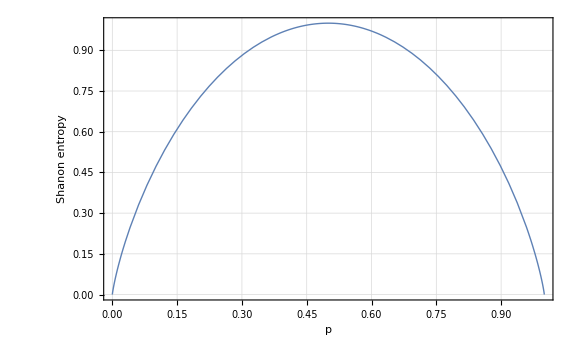

Figure 1. The Shannon entropy H({p,1−p}) associated with a binary probability distribution {p(0)=p,p(1)=1−p} of a random variable with values in {0,1}.

So far, entropy has been regarded as a measure of uncertainty. It may sound contradictory at first glance, but a valuable alternative interpretation is that entropy quantifies the information content in the state of a physical system. Suppose that we have learned value x of a random variable X. Compared to the case we did not learn the value, our knowledge of the random variable has increased. We then ask the question, “How much of information, on average, have we acquired by learning the value of X?” Since the Shannon entropy is the amount of uncertainty before we learn the value and it is the amount of uncertainty that is cleared by learning the value, the information gain is also given by the Shannon entropy. The two interpretations thus provide two alternative views of entropy: One can regard the entropy as a measure of the uncertainty before we learn the value of X. But one can also regard it as a measure of the information gained after we learn the value of X.

A basic yet significant property of the Shannon entropy is the inequality

0≤H(X)≤log d ,

where d is the number of values that X can take. The entropy becomes maximum, H(X)=log d, if and only if the probability is uniformly distributed. We defer proving the property until we introduce relative entropy since the proof is simplest by using this quantity.

Relative Entropy

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

(to be completed soon)

Mutual Information

(to be completed soon)

Data Compression

(to be completed soon)

| Related Guides
▪Quantum Computation and Quantum Information

| Related Tech Notes
▪Quantum Information Theory
▪Quantum Computation and Quantum Information with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).